# Spline Pyramids

No need for imports, independent package

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

### Test Points

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0993805,0.90062,1.,1.,1.,1.,1.,1.,0.90062,0.0993805,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

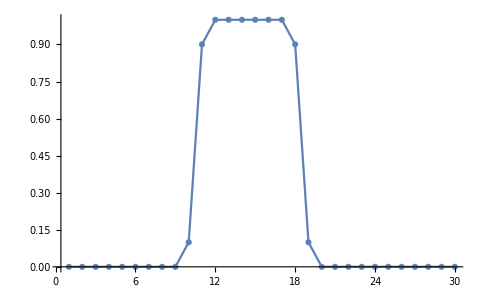

```mathematica
line=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1]
ListPlot[line,Joined->True,PlotMarkers->Automatic,PlotRange->All]
```

## Gaussian Kernel

Gaussian filter tap 5 where a={0.3, 0,6}

```mathematica
gaussianKernel[a_]:={1-a*2, 1,a*4,1,1-a*2}/4.0;

gaussianKernel::usage="
Gaussian filter tap 5 where a={0.3, 0,6}
";
```

### Test

```mathematica
gaussianKernel[0.3]
```

{0.1,0.25,0.3,0.25,0.1}

## next Pyramid’s level values

Takes values from any level and return the values of the next level
ADDS a value before and after, padding of 2 which become 1 due to averaging

```mathematica
pyrNextLevel[line_]:=Block[{d},(
d=ListConvolve[gaussianKernel[0.3],ArrayPad[line,2+2(* to get 1 extra value on each side *),"Fixed"]];
Mean/@Partition[d,2]
)];

pyrNextLevel::usage="
Takes values from any level and return the values of the next level
ADDS a value before and after, padding of 2 which become 1 due to averaging
";
```

### Test

```mathematica
pyrNextLevel[{1,2,3,4,5,6,7}]
pyrNextLevel[{1,2,3,4,5,6,7,8}]
```

{1.05,1.775,3.5,5.45,6.725}

{1.05,1.775,3.5,5.5,7.225,7.95}

### Test

```mathematica
y=pyrNextLevel[line];
line
y
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0993805,0.90062,1.,1.,1.,1.,1.,1.,0.90062,0.0993805,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,0.,0.00496902,0.234938,0.765062,0.995031,0.995031,0.765062,0.234938,0.00496902,0.,0.,0.,0.,0.}

## next Pyramid’s level coordinates

compute the X coordinates of next level based on a current level
we usually start with Range[1,lineSize] at level 0

```mathematica
pyrNextCoord[coords_]:=Block[{step,first,last,x},(
step=coords[[2]]-coords[[1]];
first=coords[[1]]-2*(step);
last=coords[[-1]]+2*(step);
x=Table[i,{i,first,last,step}];
N[Mean/@Partition[x,2]]
)];

pyrNextCoord::usage="
compute the X coordinates of next level based on a current level
we usually start with Range[1,lineSize] at level 0
";
```

### Test

```mathematica
pyrNextLevel[{1,2,3,4,5,6,7}]
pyrNextCoord[Range[1,7]]
pyrNextLevel[{1,2,3,4,5,6,7,8}]
pyrNextCoord[Range[1,8]]
```

{1.05,1.775,3.5,5.45,6.725}

{-0.5,1.5,3.5,5.5,7.5}

{1.05,1.775,3.5,5.5,7.225,7.95}

{-0.5,1.5,3.5,5.5,7.5,9.5}

### Test

```mathematica
x=pyrNextCoord[Range[1,Length[line]]]
```

{-0.5,1.5,3.5,5.5,7.5,9.5,11.5,13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5,29.5,31.5}

### Test

```mathematica
Level 0
```

0

```mathematica
y=line;
x=Range[1,Length[line]];
p0=Flatten[{x,y},{{2}{1}}]
```

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.0993805},{11,0.90062},{12,1.},{13,1.},{14,1.},{15,1.},{16,1.},{17,1.},{18,0.90062},{19,0.0993805},{20,0.},{21,0.},{22,0.},{23,0.},{24,0.},{25,0.},{26,0.},{27,0.},{28,0.},{29,0.},{30,0.}}

```mathematica
Level 1
```

Level

```mathematica
y=pyrNextLevel[y];
x=pyrNextCoord[x];
p1=Flatten[{x,y},{{2}{1}}]
```

{{-0.5,0.},{1.5,0.},{3.5,0.},{5.5,0.},{7.5,0.00496902},{9.5,0.234938},{11.5,0.765062},{13.5,0.995031},{15.5,0.995031},{17.5,0.765062},{19.5,0.234938},{21.5,0.00496902},{23.5,0.},{25.5,0.},{27.5,0.},{29.5,0.},{31.5,0.}}

```mathematica
Level 2
```

2 Level

```mathematica
y=pyrNextLevel[y];
x=pyrNextCoord[x];
p2=Flatten[{x,y},{{2}{1}}]
```

{{-3.5,0.},{0.5,0.},{4.5,0.0126165},{8.5,0.249612},{12.5,0.737772},{16.5,0.737772},{20.5,0.249612},{24.5,0.0126165},{28.5,0.},{32.5,0.}}

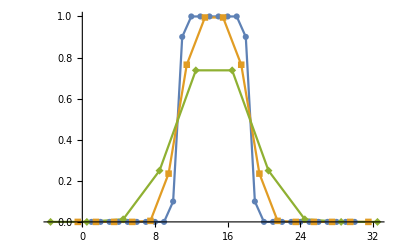

```mathematica
ListPlot[{p0,p1,p2},Joined->True,PlotMarkers->Automatic]
```

## Pyramid’s first and last coordinates

return: first and last coordinates of a specific pyramid level.
 ATENTION: we need the lineSize of level 0 to figure out the coordinates of all following levels

```mathematica
pyrCoordFirstLast[level_,lineSizeLevel0_]:=Block[{},(
Nest[pyrNextCoord,Range[1,lineSizeLevel0],level][[{1,-1}]]
)];

pyrCoordFirstLast::usage="
return: first and last coordinates of a specific pyramid level.
 ATENTION: we need the lineSize of level 0 to figure out the coordinates of all following levels 
";
```

### Test

```mathematica
pyrNextCoord[Range[1,8]]
pyrCoordFirstLast[1,8]
```

{-0.5,1.5,3.5,5.5,7.5,9.5}

{-0.5,9.5}

## Pyramid’s spline interpolation

create a spline for the line containing y values, and coords contains the x coordinates of the values
  actually, only the first and last coords are used...

```mathematica
functionGen[line_,{firstCoord_,___,lastCoord_}] := Block[
{fline}, (
fline=ListInterpolation[line, {firstCoord,lastCoord}, Method -> "Spline", InterpolationOrder -> 3];
{fline,fline'}
)];

functionGen::usage="
create a spline for the line containing y values, and coords contains the x coordinates of the values
  actually, only the first and last coords are used...
";
```

## Pyramids generation

generate all pyramid lines
pyramid factor is hard-coded at 2
We assign coordinates 1..20 to a list of 20 values in line0.

```mathematica
pyrFuncGen[line0_,maxLevel_]:=Block[{y,x},(
y=NestList[pyrNextLevel,line0,maxLevel];
x=NestList[pyrNextCoord,Range[1,Length[line0]],maxLevel];
Table[functionGen[y[[i]],x[[i]]],{i,1,Length[y]}]
)];

pyrFuncGen::usage="
Input= [Points to interpolate, max target lvl]
Output= {maxlvl+1, {f, df}}
";
```

### Test

{{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]}}

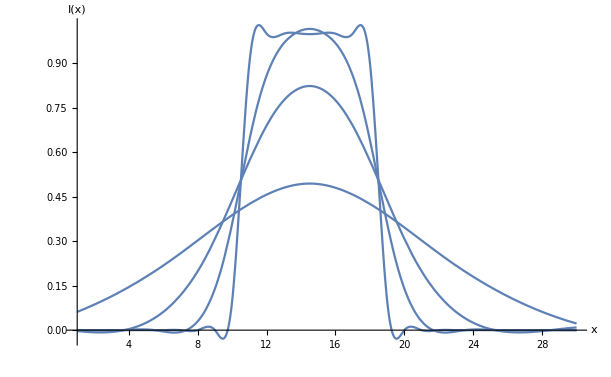

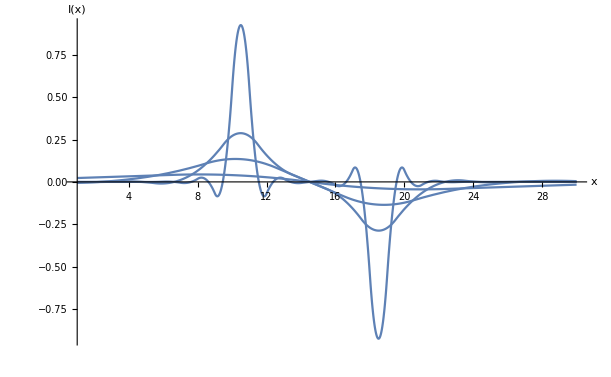

```mathematica
pyrf=pyrFuncGen[line,3]
fontsize=16;
Plot[#[[1]][x]&/@pyrf,{x,1,Length[line]},
PlotRange->All, 
AxesLabel->{Style["x",FontSize->fontsize,FontFamily->"Times", Italic],Style["I(x)",FontSize->fontsize,FontFamily->"Times", Italic]}]

Plot[#[[2]][x]&/@pyrf,{x,1,Length[line]},
PlotRange->All, 
AxesLabel->{Style["x",FontSize->fontsize,FontFamily->"Times", Italic],Style["I(x)",FontSize->fontsize,FontFamily->"Times", Italic]}]
```